```mathematica
G[z_, λ_, M_] = Exp[λ*z]Exp[-λ*(M-1)]*((1-Exp[-λ])*Exp[λ*z] + 1)^(M-2)
```

ⅇ^(-(-1+M) λ+z λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M)

```mathematica
Simplify[ⅇ^(-(-1+M) λ+λz) (1+ⅇ^λz (1-ⅇ^-λ))^(-2+M)]
```

ⅇ^(λ-M λ+λz) (1+ⅇ^λz-ⅇ^(-λ+λz))^(-2+M)

```mathematica
G[1, 1, 10]
```

ⅇ^(-9+λz) (1+(1-1/ⅇ) ⅇ^λz)^8

```mathematica
CoefficientList[Series[G[x, 1, 10], {x, 0, 20}], x]
```

{(-1+2 ⅇ)^8/ⅇ^17,((-1+2 ⅇ)^7 (-9+10 ⅇ))/ⅇ^17,18,(2-1/ⅇ)^8/(2432902008176640000 ⅇ^9)+19+((-1+ⅇ) (-1+2 ⅇ)^5 (64-151 ⅇ+88 ⅇ^2))/(266765571072000 ⅇ^17)}
 |  |  |  |

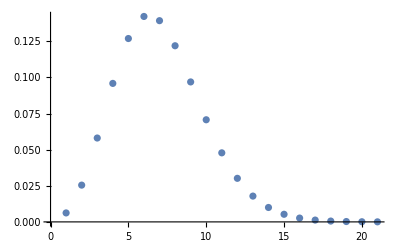

```mathematica
ListPlot[%27]
```

```mathematica
CoefficientList[Series[G[x, 2, 10], {x, 0, 30}], x]
```

{((2-1/ⅇ^2)^8)/ⅇ^18,29,(256 (1-1/ⅇ^2) (2-1/ⅇ^2)^7)/(263505041412702261046875 ⅇ^18)+(16 (2-1/1)^8)/(3952575621190533915703125 ⅇ^18)+1/ⅇ^18+25+1+(128 2 (-8+9 1))/(9086380738369043484375 ⅇ^34)+(512 (-1+ⅇ^2) (-1+2 1)^5 (64-151 ⅇ^2+88 ⅇ^4))/(3894163173586732921875 ⅇ^34)}
 |  |  |  |

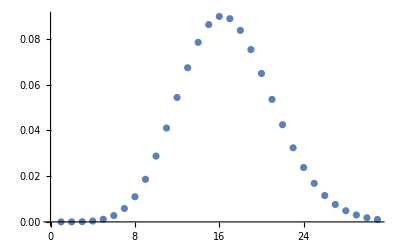

```mathematica
ListPlot[%31]
```

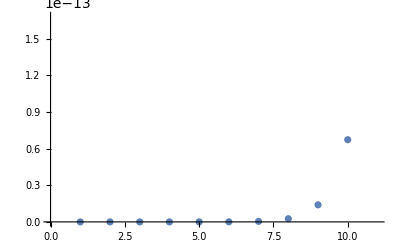

```mathematica
ListPlot[%23]
```

```mathematica
CoefficientList[%18,x]
```

{ⅇ^(λ-M λ) (2-ⅇ^-λ)^(-2+M),(ⅇ^(3 λ-M λ) (2-ⅇ^-λ)^M (1-M+ⅇ^λ M) λ)/((-1+2 ⅇ^λ)^3),(ⅇ^(3 λ-M λ) (2-ⅇ^-λ)^M (1+2 ⅇ^λ-2 ⅇ^(2 λ)-2 M+ⅇ^λ M+ⅇ^(2 λ) M+M^2-2 ⅇ^λ M^2+ⅇ^(2 λ) M^2) λ^2)/(2 (-1+2 ⅇ^λ)^4),1/(6 (-1+2 ⅇ^λ)^5)ⅇ^(3 λ-M λ) (2-ⅇ^-λ)^M (1+8 ⅇ^λ-8 ⅇ^(2 λ)-3 M-7 ⅇ^λ M+16 ⅇ^(2 λ) M-6 ⅇ^(3 λ) M+3 M^2-3 ⅇ^λ M^2-3 ⅇ^(2 λ) M^2+3 ⅇ^(3 λ) M^2-M^3+3 ⅇ^λ M^3-3 ⅇ^(2 λ) M^3+ⅇ^(3 λ) M^3) λ^3,1/(24 (-1+2 ⅇ^λ)^6)ⅇ^(-M λ) (2-ⅇ^-λ)^M (ⅇ^(3 λ) λ^4+22 ⅇ^(4 λ) λ^4-6 ⅇ^(5 λ) λ^4-32 ⅇ^(6 λ) λ^4+16 ⅇ^(7 λ) λ^4-4 ⅇ^(3 λ) M λ^4-39 ⅇ^(4 λ) M λ^4+61 ⅇ^(5 λ) M λ^4-4 ⅇ^(6 λ) M λ^4-14 ⅇ^(7 λ) M λ^4+6 ⅇ^(3 λ) M^2 λ^4+16 ⅇ^(4 λ) M^2 λ^4-59 ⅇ^(5 λ) M^2 λ^4+46 ⅇ^(6 λ) M^2 λ^4-9 ⅇ^(7 λ) M^2 λ^4-4 ⅇ^(3 λ) M^3 λ^4+6 ⅇ^(4 λ) M^3 λ^4+6 ⅇ^(5 λ) M^3 λ^4-14 ⅇ^(6 λ) M^3 λ^4+6 ⅇ^(7 λ) M^3 λ^4+ⅇ^(3 λ) M^4 λ^4-4 ⅇ^(4 λ) M^4 λ^4+6 ⅇ^(5 λ) M^4 λ^4-4 ⅇ^(6 λ) M^4 λ^4+ⅇ^(7 λ) M^4 λ^4),1/(120 (-1+2 ⅇ^λ)^7)ⅇ^(-M λ) (2-ⅇ^-λ)^M (ⅇ^(3 λ) λ^5+52 ⅇ^(4 λ) λ^5+84 ⅇ^(5 λ) λ^5-272 ⅇ^(6 λ) λ^5+136 ⅇ^(7 λ) λ^5-5 ⅇ^(3 λ) M λ^5-131 ⅇ^(4 λ) M λ^5+48 ⅇ^(5 λ) M λ^5+366 ⅇ^(6 λ) M λ^5-358 ⅇ^(7 λ) M λ^5+80 ⅇ^(8 λ) M λ^5+10 ⅇ^(3 λ) M^2 λ^5+115 ⅇ^(4 λ) M^2 λ^5-245 ⅇ^(5 λ) M^2 λ^5+35 ⅇ^(6 λ) M^2 λ^5+155 ⅇ^(7 λ) M^2 λ^5-70 ⅇ^(8 λ) M^2 λ^5-10 ⅇ^(3 λ) M^3 λ^5-30 ⅇ^(4 λ) M^3 λ^5+155 ⅇ^(5 λ) M^3 λ^5-185 ⅇ^(6 λ) M^3 λ^5+75 ⅇ^(7 λ) M^3 λ^5-5 ⅇ^(8 λ) M^3 λ^5+5 ⅇ^(3 λ) M^4 λ^5-10 ⅇ^(4 λ) M^4 λ^5-10 ⅇ^(5 λ) M^4 λ^5+40 ⅇ^(6 λ) M^4 λ^5-35 ⅇ^(7 λ) M^4 λ^5+10 ⅇ^(8 λ) M^4 λ^5-ⅇ^(3 λ) M^5 λ^5+5 ⅇ^(4 λ) M^5 λ^5-10 ⅇ^(5 λ) M^5 λ^5+10 ⅇ^(6 λ) M^5 λ^5-5 ⅇ^(7 λ) M^5 λ^5+ⅇ^(8 λ) M^5 λ^5)}

```mathematica
F[x_] = G[z, 1, 10]
```

ⅇ^(-9+λz) (1+(1-1/ⅇ) ⅇ^λz)^8

```mathematica
gen[z_, λ_, n_, M_] = Exp[-λ*(M-1)]*((1-Exp[-λ])*Exp[λ*z]+1)^(M-2)+ (1-Exp[-λ])*z^n *(1-Exp[-λ]*(1-Exp[λ*(1/z-1)]))^(M-2)
```

ⅇ^(-(-1+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M)+(1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-2+M) z^n

```mathematica
D[(ⅇ^(-(-1+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M)+(1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-2+M) z^n), z]
```

(1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-2+M) n z^(-1+n)+ⅇ^((1-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (-2+M) λ-ⅇ^(-λ+(-1+1/z) λ) (1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-3+M) (-2+M) z^(-2+n) λ

```mathematica
temporary[λ_, n_, M_] = (1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-2+M) n z^(-1+n)+ⅇ^((1-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (-2+M) λ-ⅇ^(-λ+(-1+1/z) λ) (1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-3+M) (-2+M) z^(-2+n) λ
```

(1-ⅇ^-λ) n-ⅇ^-λ (1-ⅇ^-λ) (-2+M) λ+ⅇ^(λ+(1-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-3+M) (-2+M) λ

```mathematica
temporary[1, 10, 100]
```

10 (1-1/ⅇ)-(98 (1-1/ⅇ))/ⅇ+(98 (1-1/ⅇ) (1+(1-1/ⅇ) ⅇ)^97)/ⅇ^98

```mathematica
N[10 (1-1/ⅇ)-(98 (1-1/ⅇ))/ⅇ+(98 (1-1/ⅇ) (1+(1-1/ⅇ) ⅇ)^97)/ⅇ^98]
```

6.32121

```mathematica
gen[1, 2,10, 100]
```

1-1/ⅇ^2+((1+(1-1/ⅇ^2) ⅇ^2)^98)/ⅇ^198

```mathematica
N[1-1/ⅇ^2+((1+(1-1/ⅇ^2) ⅇ^2)^98)/ⅇ^198]
```

1.

```mathematica
N[1-1/ⅇ^2+(1+(1-1/ⅇ^2) ⅇ^2)/ⅇ^198]
```

0.864665

```mathematica
Simplify[ⅇ^(-(-1+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))+(1-ⅇ^-λ) (1-ⅇ^-λ (1-ⅇ^((-1+1/z) λ)))^(-2+M) z^n]
```

ⅇ^(-M λ) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ))+(1-ⅇ^-λ) (1-ⅇ^-λ+ⅇ^((-2+1/z) λ))^(-2+M) z^n

```mathematica
D[(ⅇ^(-M λ) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ))+(1-ⅇ^-λ) (1-ⅇ^-λ+ⅇ^((-2+1/z) λ))^(-2+M) z^n), z]
```

(1-ⅇ^-λ) (1-ⅇ^-λ+ⅇ^((-2+1/z) λ))^(-2+M) n z^(-1+n)-ⅇ^((-2+1/z) λ) (1-ⅇ^-λ) (1-ⅇ^-λ+ⅇ^((-2+1/z) λ))^(-3+M) (-2+M) z^(-2+n) λ+ⅇ^(-M λ) (-ⅇ^(z λ) λ+ⅇ^(λ+z λ) λ)

```mathematica
CoefficientList[Series[gen[1-x, 0.2, 8, 10], {x, 0, 10}], x]
```

{1.,-1.45015,3.62705,-6.05991,6.43581,-4.39895,1.88702,-0.464242,0.0501481,0.0000113625,0.0000131204}

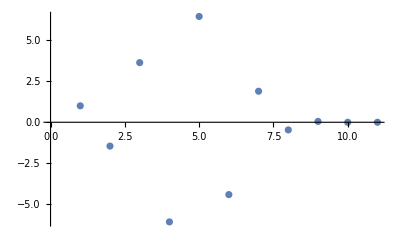

```mathematica
ListPlot[%47]
```

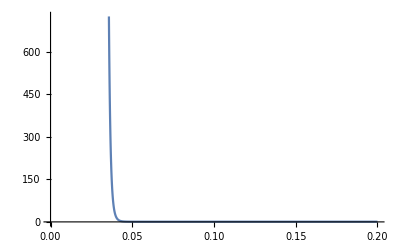

```mathematica
Plot[gen[x, 0.2, 10, 10], {x, 0, 0.2}]
```